```mathematica
file="D:\\Software\\Python Meas\\QControl_3.1\\testonetone.dat";
Import[file][[1]]
data=Import[file][[2;;]];
```

{freq,demod_AI0,demod_AQ0,demod_BI0,demod_BQ0}

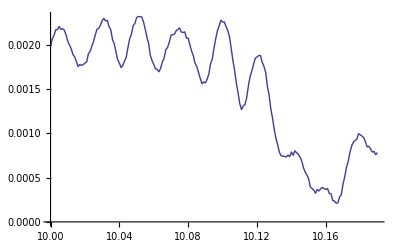

```mathematica
ListLinePlot[{#[[1]],Abs[#[[2]]+I#[[3]]]}&/@data]
```

```mathematica
x=#[[2]]#[[4]]+#[[3]]#[[5]]&/@data;
y=#[[2]]#[[5]]-#[[3]]#[[4]]&/@data;
```